## The Shooting Method (application to energy levels of the simple harmonic oscillator and other problems of a particle in a potential minimum)

## Introduction

In the previous handout we found the eigenvalues of a quantum particle in a potential well where the potential vanishes for |x| greater than some value, which has the advantage that we know the wavefunction exactly in this large |x| region.  The same method can be used for problems where the potential, while not exactly zero at large |x|, is sufficiently close to zero that the error in assuming it vanishes is negligible.

Here we give a generalization of this approach to problems where the potential does not have to tend to zero at large |x|. This more general approach is often called the shooting method . This handout is very similar to the earlier one except for the way it handles the boundary conditions at large |x|. As before, we consider potentials which are symmetric, i.e. even functions of x, so the eigenfunctions have either even or odd parity. We will consider solutions of each parity separately.

## Setting up the Problem of the Simple Harmonic Oscillator

As an illustration,we take the simple harmonic oscillator (SHO) potential with ℏ=ω=m=1,for which there is an analytic solution, discussed in all books on quantum mechanics. The energy levels are

E_n= n + 1/2    ,    (n=0, 1, 2, ... )

First we set up the potential and plot it.

```mathematica
Clear ["Global`*"]
```

```mathematica
v0 = 1;
```

```mathematica
v[x_] :=v0  x^2 /2
```

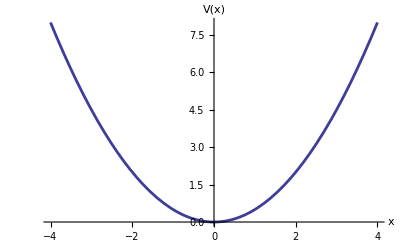

```mathematica
Plot[v[x], {x, -4, 4} ,AxesStyle -> AbsoluteThickness[1],  AxesLabel -> {"x", "V(x)"}]
```

We define the Schrodinger equation using a delayed assignment, ":=", since we will only use it later:

```mathematica
eqn[en_] := u''[x] + 2(en - v[x])u[x]
```

(we call the wavefunction u(x) here.) Note that the Schrodinger equation is written for a general potential V(x), so we will trivially be able consider other potentials as well.  We will solve the equation in the range -L ≤ x ≤ 0, and choose L such that V(x) >> E at x=-L, i.e. x = -L is well to the left of the "turning point" where V(x) = E. We take L = 4, which is fine for the lowest level. However we will need to increase L to get the higher levels accurately.

```mathematica
L = 4;
```

At x = -L, we take, arbitrarily,  u(-L) = 0, u'(-L) = 1. This corresponds to a linear superposition of the solution which decays exponentially to the left and the one which increases exponentially. We just want the solution which decreases exponentially to the left. However, if L is deep inside the region where V(x) > E the error will be negligible since we integrate to the right (not the left) and so the unwanted solution will be exponentially surpressed as we integrate to the right towards the negative-x turning point.

We set up the calculation of the wavefunction in the region between -L and 0, matching the function and its derivative to the specified values at x = -L.

```mathematica
wavefunc[en_] := NDSolve[{ eqn[en] == 0, u[-L] ==  0, 
					u'[-L] == 1}, u, {x, -L, 0} ]
```

Note that "wavefunc[en_]"  will given as a replacement rule in the form "{{u→InterpolatingFunction[{{-0.5,0.5}},"<>"]}}". In order to directly access the wavefunction we define a function, called sol[x, en], which applies the replacement rule, and removes one of the sets of curly brackets by taking the first element of the list.

```mathematica
sol[x_?NumericQ, en_?NumericQ] := u[x] /.wavefunc[en][[1]]
```

As before we have added the hieroglyphics 
                             ?NumericQ 
after the arguments of sol. This is necessary in  Mathematica version 5 and later when the solution is put into FindRoot below to determine the energy eigenvalue.

It is also convenient to define a function for the derivative of the wave function (since we will be requiring that this is zero at x = 0 for the even parity solutions):

```mathematica
solprime[x_?NumericQ, en_?NumericQ] := u'[x] /.wavefunc[en][[1]]
```

## Even Parity Solution

We now find an eigenvalue corresponding to an even parity eigenfunction. We use the "FindRoot" command to locate the eigenvalue and give it two starting values. The boundary condition is that the derivative of the wavefunction is zero at x = 0:

```mathematica
evalue = en /. FindRoot [  solprime[0, en] ,{en, 0, 1} ]
```

0.5

This agrees with the known ground state energy of the simple harmonic oscillator, E_0= 1/2.

Now we want the eigenfunction coresponding to our eigenvalue. Since we now have the eigenvalue, we do not  want to keep recalculating  the wavefunction so we define a function "efunc" with immediate assignment, where we input the eigenvalue for the energy:

```mathematica
efunc[x_] = u[x] /. wavefunc[evalue][[1]];
```

We have now obtained the wavefunction in for x < 0. We now also define it for x > 0 (remembering that it's even) and collect these functions into a single (not yet normalized) function ψnn[x_], which can then easily be plotted:

```mathematica
ψnn[x_] := efunc[x] /; x≤ 0 ;
```

```mathematica
ψnn [x_] := efunc[-x] /; x > 0 ;
```

We now normalize the wavefunction,

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -L, L} ] ];
```

```mathematica
ψ[x_] := ψnn[x] / normconst;
```

and then plot it:

```mathematica
fig = Plot[ψ[x], {x, -L, L}, AxesLabel -> {"x", "ψ"},PlotRange -> {0, 1} ];
```

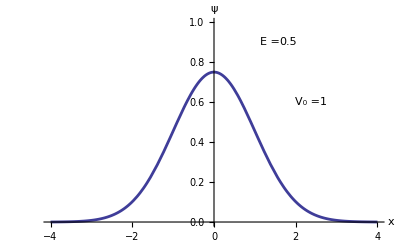

```mathematica
Show[fig,  Graphics [ { 
			Text[evalue, {1.6, 0.9}, {-1, 0} ] ,
Text[ "E = ", {1.6, 0.9}, {1, 0}  ],
			Text[  v0, {2.6, 0.6}, {-1, 0} ] ,
Text[ "V_0 = ", {2.6, 0.6}, {1, 0}  ] } ] ]
```

We see that there are no nodes (zeroes) in the wavefunction which means, since we are in one dimension, that it is the ground state.

## Odd Parity Solution

Now we look at odd-parity  solutions.

We repeat the previous calculation of the eigenvalue, and calculate the eigenfunction, which is then normalized and plotted. We give different initial guesses for the eigenvalue from what we took for the even parity solution and also take a somewhat larger value for L, in order to get an accurate answer for this state which has higher energy than the even parity solution discussed in the previous section.

```mathematica
L = 5;
```

The boundary condition is now that the wavefunction vanishes at the origin:

```mathematica
evalue =en /. FindRoot [ sol[0, en],{en, 1, 3} ]
```

1.5

This agrees with the known energy of the first excited state of the simple harmonic oscillator, E_1= 3/2.

Next we calculate the eigenfunction,

```mathematica
efunc[x_] = u[x] /. wavefunc[evalue][[1]];
```

redefine it for x > 0 (noting that it is now odd rather than even)

```mathematica
ψnn [x_] := -efunc[-x] /; x > 0
```

and recompute the normalization constant

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -L, L} ] ];
```

Everything else is the same as for the even-parity eigenfunction and used delayed assignment. Hence we can now plot the eigenfunction

```mathematica
fig = Plot[ψ[x], {x, -L, L}, AxesLabel -> {"x", "ψ"} ];
```

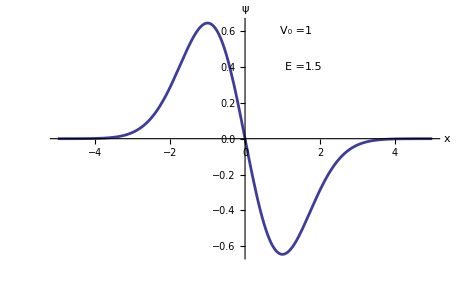

```mathematica
Show[fig,  Graphics [ { 
			Text[evalue, {1.6, 0.4}, {-1, 0} ] ,
Text[ "E = ", {1.6, 0.4}, {1, 0}  ],
			Text[  v0, {1.6, 0.6}, {-1, 0} ] ,
Text[ "V_0 = ", {1.6, 0.6}, {1, 0}  ]} ] ]
```

The wavefunction is smooth and has only one node, showing that it is the lowest energy odd-parity  eigenstate.

The "shooting method" described in this handout can be applied to essentially any quantum well problem in one dimension with a symmetric potential.  The main thing is to ensure that L is far enough into the region where the solution is exponentially decaying that the boundary conditions applied at x = -L  do not introduce a noticeable amount of the "wrong" solution in the x-region  of interest. It is also straightforward to generalize the method to the case of a non-symmetric potential.

## Anharmonic Oscillator

Now we consider a problem for which there is no analytic solution; an oscillator with a quartic potential, in addition to the quadratic potential:

```mathematica
Clear[v]
```

```mathematica
v[x_] := x^2 / 2 + λ x^4
```

We set the coefficient of the quartic potential to equal 0.2.

```mathematica
λ = 0.2;
```

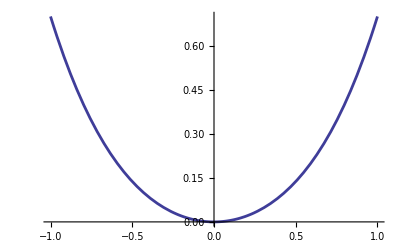

```mathematica
Plot[v[x], {x, -1, 1}]
```

```mathematica
L = 4
```

4

We look for the lowest eigenvalue, for which the eigenfunction will be even.

```mathematica
evalue =en /. FindRoot [ solprime[0, en],{en, 0, 1} ]
```

0.602405

```mathematica
efunc[x_] = u[x] /. wavefunc[evalue][[1]];
```

```mathematica
ψnn [x_] := efunc[-x] /; x > 0
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -L, L} ] ];
```

```mathematica
fig = Plot[ψ[x], {x, -L, L}, AxesLabel -> {"x", "ψ"} ];
```

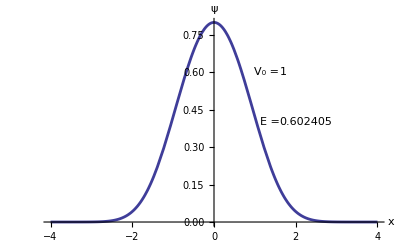

```mathematica
Show[fig,  Graphics [ { 
			Text[evalue, {1.6, 0.4}, {-1, 0} ] ,
Text[ "E = ", {1.6, 0.4}, {1, 0}  ],
			Text[  v0, {1.6, 0.6}, {-1, 0} ] ,
Text[ "V_0 = ", {1.6, 0.6}, {1, 0}  ]} ] ]
```

Hence the lowest eigenvalue is 0.602405, which compares with 0.5 for the quadratic potential.

The first excited even eigenstate can be obtained from

```mathematica
evalue =en /. FindRoot [ solprime[0, en],{en, 2.5, 3.5} ]
```

3.5363

```mathematica
efunc[x_] = u[x] /. wavefunc[evalue][[1]];
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -L, L} ] ];
```

and then plotted

```mathematica
fig = Plot[ψ[x], {x, -L, L}, AxesLabel -> {"x", "ψ"}];
```

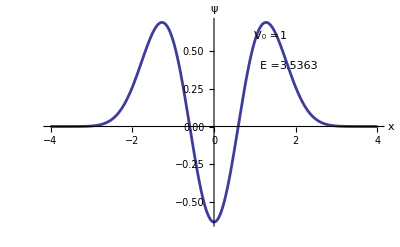

```mathematica
Show[fig,  Graphics [ { 
			Text[evalue, {1.6, 0.4}, {-1, 0} ] ,
Text[ "E = ", {1.6, 0.4}, {1, 0}  ],
			Text[  v0, {1.6, 0.6}, {-1, 0} ] ,
Text[ "V_0 = ", {1.6, 0.6}, {1, 0}  ]} ] ]
```

As expected there are two nodes.

We can also get the lowest odd eigenstate:

```mathematica
evalue =en /. FindRoot [ sol[0, en],{en, 1, 2} ]
```

1.95054

```mathematica
efunc[x_] = u[x] /. wavefunc[evalue][[1]];
```

```mathematica
ψnn [x_] := -efunc[-x] /; x > 0
```

```mathematica
normconst = Sqrt[ NIntegrate [ ψnn[x]^2, {x, -L, L} ] ];
```

```mathematica
fig = Plot[ψ[x], {x, -L, L}, AxesLabel -> {"x", "ψ"} ];
```

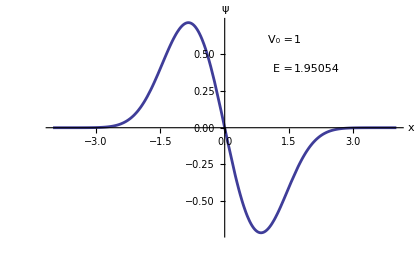

```mathematica
Show[fig,  Graphics [ { 
			Text[evalue, {1.6, 0.4}, {-1, 0} ] ,
Text[ "E = ", {1.6, 0.4}, {1, 0}  ],
			Text[  v0, {1.6, 0.6}, {-1, 0} ] ,
Text[ "V_0 = ", {1.6, 0.6}, {1, 0}  ]} ] ]
```

We see that unlike the simple harmonic oscillator, the energy levels, 0.602405, 1.95054, 3.5363, ... , are not evenly spaced.